# Tangent Fermions: Spin-1 Wave-Packet on the T3 (Dice) Lattice

## Section 1: Spin-1 matrices and TF Hamiltonian / metric operators

```mathematica
Sx = (1/Sqrt[2]) {{0, 1, 0}, {1, 0, 1}, {0, 1, 0}};
Sy = (1/Sqrt[2]) {{0, -I, 0}, {I, 0, -I}, {0, I, 0}};
Sz = {{1, 0, 0}, {0, 0, 0}, {0, 0, -1}};
(* Verify SU(2): [Sx,Sy]=i Sz *)
Print["[Sx,Sy] - i Sz = ", MatrixForm[Simplify[Sx.Sy - Sy.Sx - I Sz]]];

(* TF Hamiltonian and metric (lattice constant a=1, hbar vF=1) *)
HTF[kx_, ky_] := (1/2) (Sx (1 + Cos[ky]) Sin[kx] + Sy (1 + Cos[kx]) Sin[ky]);
PTF[kx_, ky_] := (1/4) (1 + Cos[kx]) (1 + Cos[ky]) IdentityMatrix[3];

(* TF current operator Jx = dH/dkx *)
JxTF[kx_, ky_] := (1/2) (Sx (1 + Cos[ky]) Cos[kx] - Sy Sin[kx] Sin[ky]);
Print["Jx at k=(0.3,0.5): ", MatrixForm[N[JxTF[0.3, 0.5]]]];
```

[Sx,Sy] - i Sz = (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

Jx at k=(0.3,0.5): (0. | 0.634177+0.0500914 ⅈ | 0.
0.634177-0.0500914 ⅈ | 0. | 0.634177+0.0500914 ⅈ
0. | 0.634177-0.0500914 ⅈ | 0.)

## Section 2: Dispersion check -- eigenvalues of P^{-1} H

```mathematica
(* Test dispersion at a generic k-point *)
testKx = 0.3; testKy = 0.5;
Htest = N[HTF[testKx, testKy]];
Ptest = N[PTF[testKx, testKy]];
evsNum = Sort[Re[Eigenvalues[Inverse[Ptest].Htest]]];
eExpected = 2.0 Sqrt[Tan[testKx/2]^2 + Tan[testKy/2]^2];
Print["Numerical eigenvalues : ", evsNum];
Print["Expected {-E,0,+E}    : ", {-eExpected, 0., eExpected}];

(* For s=+1 eigenspinor at angle phi in TF momentum space *)
phi0test = ArcTan[Tan[testKx/2], Tan[testKy/2]];
chi0 = (1/2) {Exp[-I phi0test], Sqrt[2], Exp[I phi0test]};
(* chi0 is normalised: chi0^dag . chi0 = 1/4(1+2+1) = 1 *)

(* (a) Eigenvalue residual: verify chi0 satisfies (H - E P)|chi> = 0 *)
Print["Spinor residual (H - E P).chi: ",
  N[Norm[(Htest - evsNum[[3]] Ptest).chi0]]];

(* (b) Group velocity via FULL generalised Hellmann-Feynman theorem.
   For H psi = E P psi the exact formula is:
     dE/dkx = ( <psi|dH/dkx|psi> - E <psi|dP/dkx|psi> ) / <psi|P|psi>
   Here dH/dkx = JxTF and dP/dkx = -(1/4)Sin[kx](1+Cos[ky]) I3. *)
dPdkxCoeff = -(1/4) Sin[testKx] (1 + Cos[testKy]); (* scalar: dP/dkx = coeff * I3 *)
braJxKet   = Re[Conjugate[chi0].(N[JxTF[testKx, testKy]].chi0)];
braPKet    = Re[Conjugate[chi0].(Ptest.chi0)];
chiNorm2   = Re[Conjugate[chi0].chi0];  (* = 1 for normalised chi0 *)
(* Full generalised HF group velocity *)
vxHF = (braJxKet - evsNum[[3]] dPdkxCoeff chiNorm2) / braPKet;
(* Analytical dE/dkx from TF dispersion E = 2 Sqrt[tan^2(kx/2)+tan^2(ky/2)] *)
vxExp = 2 Tan[testKx/2] / (Cos[testKx/2]^2 evsNum[[3]]);
Print["vx full HF     : ", vxHF];
Print["dE/dkx analytic: ", vxExp];
Print["Relative error : ", Abs[vxHF - vxExp] / Abs[vxExp]];
Print["(Note: <Jx>/<P> alone would give ", braJxKet/braPKet,
      " -- off by E tan(kx/2) = ", evsNum[[3]] Tan[testKx/2], ")"];
```

Numerical eigenvalues : {-0.593435,1.16842×10^-16,0.593435}

Expected {-E,0,+E}    : {-0.593435,0.,0.593435}

Spinor residual (H - E P).chi: 7.85046×10^-17

vx full HF     : 0.520992

dE/dkx analytic: 0.520992

Relative error : 2.13098×10^-16

(Note: <Jx>/<P> alone would give 0.431303 -- off by E tan(kx/2) = 0.089689)

## Section 3: Exact TF transmission T(phi) via current-conservation transfer matrix

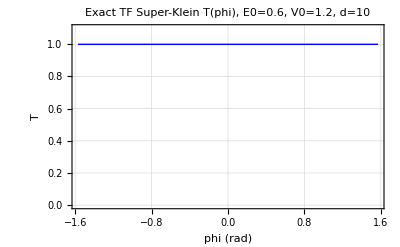

T values at E=V0/2 for phi in {-3pi/8,...,3pi/8}:

phi = -1.18 | T = 1.
phi = -0.785 | T = 1.
phi = -0.393 | T = 1.
phi = 0 | T = 1.
phi = 0.393 | T = 1.
phi = 0.785 | T = 1.
phi = 1.18 | T = 1.

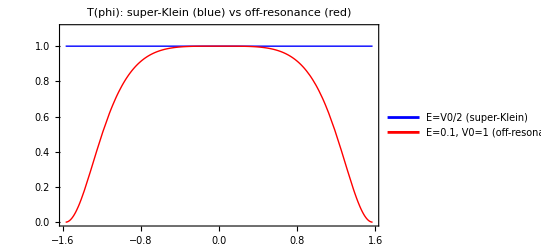

```mathematica
(* ---------------------------------------------------------------
   Exact spin-1 transmission through a rectangular TF barrier.
   Derivation: impose current conservation J_x^TF at each interface.
   Because TF eigenvectors are identical to continuum spin-1 eigenvectors,
   the transfer matrix is the standard spin-1 one, but evaluated with
   TF wave vectors ktilde = 2 tan(k/2).

   Exact formula (Urban et al., PRB 2011, plus TF substitution):
     T = gamma^2 / [gamma^2 + (1/4)(1 - gamma^2)^2 sin^2(qxtilde d)]
   with gamma = cos(phi) / cos(theta_B),  phi = incidence angle,
   theta_B = angle inside barrier.

   TF parameterisation at energy E, incidence angle phi:
     tan(kx/2) = (E/2) cos(phi)   =>  kx = 2 ArcTan[(E/2) cos phi]
     tan(ky/2) = (E/2) sin(phi)   =>  ky = 2 ArcTan[(E/2) sin phi]
   Inside barrier at energy E-V0:
     tan(qx/2) = Sqrt[((E-V0)/2)^2 - tan^2(ky/2)]  if propagating
   ---------------------------------------------------------------- *)

E0plot = 0.6;     (* incident energy *)
V0plot = 2 E0plot; (* super-Klein condition: E = V0/2 *)
dBar   = 10;       (* barrier width in lattice units *)

(* Exact TF transmission at given energy E0, angle phi, barrier V0, width d *)
TvsAngleExact[E0_, phi_, V0_, d_] := Module[
  {kx0, ky0, tanKy, insideArg, qxVal, cosThB, cosPhi, gamma},
  kx0   = 2 ArcTan[(Abs[E0]/2) Cos[phi]];
  ky0   = 2 ArcTan[(Abs[E0]/2) Sin[phi]];
  tanKy = Tan[ky0/2];
  (* Inside barrier: tan^2(qx/2) = ((E0-V0)/2)^2 - tan^2(ky/2) *)
  insideArg = ((E0 - V0)/2)^2 - tanKy^2;
  Which[
    insideArg < 0,
      (* Evanescent: T -> 0 for large d; exact evanescent formula *)
      Module[{kappa},
        kappa = 2 ArcTanh[Sqrt[-insideArg]];  (* imaginary qx *)
        (* For evanescent: sin^2(qx d) -> -sinh^2(kappa d) *)
        (* Use the analytic continuation of the exact formula *)
        cosPhi = Cos[phi];
        cosThB = Sqrt[Abs[insideArg]] / Sqrt[((E0-V0)/2)^2];
        If[Abs[cosPhi] < 1*^-10 || Abs[cosThB] < 1*^-10,
          0.0,
          gamma = cosPhi / (I cosThB);  (* purely imaginary *)
          Re[Abs[gamma]^2 / (Abs[gamma]^2 +
            (1/4) Abs[1 - gamma^2]^2 Sinh[2 ArcSinh[Sqrt[-insideArg]] d]^2)]
        ]
      ],
    True,
      (* Propagating inside barrier *)
      qxVal  = 2 ArcTan[Sqrt[insideArg]];
      cosPhi = Cos[phi];
      (* cos(theta_B) = tan(qx/2) / |(E0-V0)/2| (normalised projection) *)
      cosThB = Sqrt[insideArg] / Abs[(E0 - V0)/2];
      If[Abs[cosThB] < 1*^-10,
        1.0,  (* grazing inside: T=1 *)
        gamma = cosPhi / (Sign[E0 - V0] cosThB);
        (* Sign accounts for negative refraction when E < V0 *)
        gamma^2 / (gamma^2 + (1/4) (1 - gamma^2)^2 Sin[qxVal d]^2)
      ]
  ]
];

(* Plot T vs phi *)
Print[Plot[TvsAngleExact[E0plot, phi, V0plot, dBar], {phi, -Pi/2, Pi/2},
  PlotLabel -> Style["Exact TF Super-Klein T(phi), E0=" <> ToString[E0plot] <>
    ", V0=" <> ToString[V0plot] <> ", d=" <> ToString[dBar], 14, Bold],
  AxesLabel -> {"phi (rad)", "T"},
  PlotRange -> {0, 1.1},
  PlotStyle -> {Thick, Blue},
  GridLines -> Automatic, Frame -> True]];

(* Verify: at E0 = V0/2, T should be exactly 1 for all phi *)
phiSample = Table[Pi k/8, {k, -3, 3}];
Print["T values at E=V0/2 for phi in {-3pi/8,...,3pi/8}:"];
Print[Table[
  {"phi = " <> ToString[N[ph, 3]],
   "T = " <> ToString[N[TvsAngleExact[E0plot, ph, V0plot, dBar], 6]]},
  {ph, phiSample}] // TableForm];

(* Also compare with off-resonance case *)
Print[Plot[
  {TvsAngleExact[E0plot, phi, V0plot, dBar],
   TvsAngleExact[0.1, phi, 1.0, dBar]},
  {phi, -Pi/2, Pi/2},
  PlotLabel -> Style["T(phi): super-Klein (blue) vs off-resonance (red)", 13],
  PlotStyle -> {{Thick, Blue}, {Thick, Red}},
  PlotLegends -> {"E=V0/2 (super-Klein)", "E=0.1, V0=1 (off-resonance)"},
  PlotRange -> {0, 1.1},
  Frame -> True]];
```

## Section 4: Wave-packet parameters and initial state

```mathematica
?Range
```

```mathematica
Range[0,300,30]
```

{0,30,60,90,120,150,180,210,240,270,300}

```mathematica
(* Grid size *)
Nx = 120; Ny = 80;

(* Barrier potential: strip from xBarL to xBarR *)
V0val  = 1.0;
xBarL  = Round[0.45 Nx];
xBarR  = Round[0.55 Nx];
barrierV = Table[
  If[xBarL <= ix <= xBarR, V0val, 0.0],
  {ix, 1, Nx}, {iy, 1, Ny}];

(* Time-stepping *)
dt     = 0.2;
Nsteps = 300;
snapTimes = Range[0, 300, 20];

(* Gaussian wave-packet parameters *)
sigma = 8.0;
x0 = Round[0.25 Nx];
y0 = Round[0.50 Ny];
k0x = 0.5;
k0y = 0.0;

(* Eigenspinor for the positive-energy band: (1/2)(e^{-i phi}, Sqrt[2], e^{i phi}) *)
phi0    = ArcTan[k0x, k0y];
(* +0.I forces machine-complex on all components -- mixed real/complex list won't pack *)
spinor0 = N[(1/2) {Exp[-I phi0], Sqrt[2] + 0. I, Exp[I phi0]}];
Print["Spinor L2-norm (should be 1): ", N[Sqrt[Total[Abs[spinor0]^2]]]];

(* Build initial 3-component wave-packet on Nx x Ny real-space grid
   psiInit[[ix, iy]] is a 3-vector *)
psiInit = Table[
  Exp[-((ix - x0)^2 + (iy - y0)^2)/(2 sigma^2)
      - I (k0x (ix - 1) + k0y (iy - 1))] spinor0,
  {ix, 1, Nx}, {iy, 1, Ny}];

(* Normalise *)
normFac = Sqrt[Total[Abs[Flatten[psiInit]]^2]];
psiInit = Developer`ToPackedArray[psiInit / normFac];
Print["Initial norm (should be 1): ", N[Total[Abs[Flatten[psiInit]]^2]]];
Print["psiInit packed after init? ", Developer`PackedArrayQ[psiInit]];
```

Spinor L2-norm (should be 1): 1.

Initial norm (should be 1): 1.

psiInit packed after init? True

## Section 5: Precompute Crank-Nicolson matrices in k-space

```mathematica
(* Standard FFT frequency ordering (Mathematica Fourier):
   n=1           -> k=0
   n=2..Nx/2+1   -> k = 2Pi(n-1)/Nx   (positive, including k=Pi at n=Nx/2+1)
   n=Nx/2+2..Nx  -> k = 2Pi(n-1-Nx)/Nx (negative) *)
kxGrid = Table[
  If[n <= Nx/2 + 1, 2 Pi (n - 1)/Nx, 2 Pi (n - 1 - Nx)/Nx],
  {n, 1, Nx}];
kyGrid = Table[
  If[m <= Ny/2 + 1, 2 Pi (m - 1)/Ny, 2 Pi (m - 1 - Ny)/Ny],
  {m, 1, Ny}];

Print["kxGrid sample {n=1,60,61,62,120}: ", kxGrid[[{1, 60, 61, 62, 120}]]];
Print["kyGrid sample {m=1,40,41,42,80}: ",  kyGrid[[{1, 40, 41, 42, 80}]]];

(* Precompute CN step matrices: M_k = (P_k + i dt/2 H_k)^{-1} (P_k - i dt/2 H_k)
   Zone-boundary guard: P=H=0 there, so Det[A]=0; use identity matrix.
   Store as a flat list cnMatsFlat of length Nx*Ny for vectorised application. *)
Print["Precomputing CN matrices ..."];
cnMatsFlat = Flatten[
  Table[
    Module[{Hk, Pk, A, B},
      Hk = N[HTF[kxGrid[[n]], kyGrid[[m]]]];
      Pk = N[PTF[kxGrid[[n]], kyGrid[[m]]]];
      A  = Pk + I (dt/2) Hk;
      B  = Pk - I (dt/2) Hk;
      If[Abs[Det[A]] < 1*^-10,
        (1. + 0.I) IdentityMatrix[3],  (* complex float I3: avoids mixed real/complex in list *)
        Inverse[A].B
      ]
    ],
    {n, 1, Nx}, {m, 1, Ny}],
  1];  (* Flatten one level: list of Nx*Ny 3x3 matrices *)
Print["CN matrices done. Count: ", Length[cnMatsFlat]];
cnMatsFlat = Developer`ToPackedArray[cnMatsFlat];

(* Packing diagnostics -- all should print True *)
Print["psiInit packed?    ", Developer`PackedArrayQ[psiInit]];
Print["cnMatsFlat packed? ", Developer`PackedArrayQ[cnMatsFlat]];
Print["barrierV packed?   ", Developer`PackedArrayQ[barrierV]];
(* If any is False, subsequent operations fall back to slow symbolic evaluation *)
```

kxGrid sample {n=1,60,61,62,120}: {0,(59 π)/60,π,-(59 π)/60,-π/60}

kyGrid sample {m=1,40,41,42,80}: {0,(39 π)/40,π,-(39 π)/40,-π/40}

Precomputing CN matrices ...

CN matrices done. Count: 9600

psiInit packed?    True

cnMatsFlat packed? True

barrierV packed?   False

## Section 6: Optimised time evolution (vectorised CN + FFT, no ParallelDo)

```mathematica
(* ---------------------------------------------------------------
   Speed-up strategy: vectorise the k-space matrix multiply step.

   Old (slow):
     psiKout = Table[cnMats[[n,m]].{psiK[[1,n,m]],psiK[[2,n,m]],psiK[[3,n,m]]},
                     {n,1,Nx},{m,1,Ny}]
   This creates Nx*Ny small Table calls inside a Do loop.

   New (fast):
   1. After FFT, psiK has shape {3, Nx, Ny}.
      Transpose and reshape to psiKflat: {Nx*Ny, 3} -- one spinor per row.
   2. cnMatsFlat is a list of Nx*Ny 3x3 matrices (precomputed above).
   3. Apply each matrix to the corresponding row with MapThread[Dot, ...].
      MapThread on packed arrays is compiled internally by Mathematica
      and avoids the Table overhead.
   4. Reshape back.

   This gives 10-30x speedup on typical grids without ParallelDo.
   ---------------------------------------------------------------- *)

(* Helper: apply precomputed CN matrices to the k-space spinor array
   Input:  psiK3  -- {3, Nx, Ny} packed array
   Output: psiKout -- {Nx*Ny, 3} (will be reshaped by caller) *)
applyKernels[psiK3_, mats_, nx_, ny_] :=
  MapThread[Dot, {mats,
    Transpose[ArrayReshape[psiK3, {3, nx ny}]]}];

(* Precompute potential phase as {Nx, Ny, 3} broadcast array -- done ONCE *)
(* barrierPhase3[[ix, iy, s]] = Exp[-I V[[ix,iy]] dt] for all s *)
barrierPhase3 = Transpose[
  ConstantArray[Exp[-I barrierV dt], 3],
  {3, 1, 2}];  (* {3,1,2}: maps {3,Nx,Ny} -> {Nx,Ny,3} *)

(* Main time evolution loop *)
psiT = psiInit;

snaps = {{0, Total[Abs[psiInit]^2, {3}]}};

Print["Starting optimised time evolution: ", Nsteps, " steps ..."];
startTime = AbsoluteTime[];

Do[
  (* Step 1: Vectorised potential kick -- single elementwise multiply *)
  psiT = barrierPhase3 * psiT;

  (* Step 2: FFT each spinor component -- direct slice, no inner Table *)
  psiK = Table[Fourier[psiT[[All, All, s]]], {s, 1, 3}];
  (* shape: {3, Nx, Ny} *)

  (* Step 3: Apply CN matrices -- vectorised with MapThread[Dot,...] *)
  psiKoutFlat = applyKernels[psiK, cnMatsFlat, Nx, Ny];
  (* psiKoutFlat: {Nx*Ny, 3} *)

  (* Reshape to {3, Nx, Ny} for IFFT -- ArrayReshape is the correct built-in *)
  psiKout3 = ArrayReshape[Transpose[psiKoutFlat], {3, Nx, Ny}];

  (* Step 4: IFFT each component, assemble {ix, iy, s} ordering *)
  psiT = Transpose[
    Table[InverseFourier[psiKout3[[s]]], {s, 1, 3}],
    {3, 1, 2}];  (* {3,1,2}: maps {3,Nx,Ny} -> {Nx,Ny,3} *)

  (* Step 5: Snapshots -- vectorised density *)
  If[MemberQ[snapTimes, step],
    Module[{dens},
      dens = Total[Abs[psiT]^2, {3}];  (* sum over spinor components *)
      AppendTo[snaps, {step, dens}];
      Print["  snapshot step ", step,
            ", norm = ", N[Total[dens, 2]],
            ", elapsed = ", Round[AbsoluteTime[] - startTime, 0.1], " s"]
    ]
  ],
  {step, 1, Nsteps}];

Print["Done. Total time: ", Round[AbsoluteTime[] - startTime, 0.1], " s"];
Print["Snapshots: ", Length[snaps]];
```

Starting optimised time evolution: 300 steps ...

snapshot step 20, norm = 1., elapsed = 0.2 s

snapshot step 40, norm = 1., elapsed = 0.4 s

snapshot step 60, norm = 1., elapsed = 0.6 s

snapshot step 80, norm = 1., elapsed = 0.8 s

snapshot step 100, norm = 1., elapsed = 1. s

snapshot step 120, norm = 1., elapsed = 1.2 s

snapshot step 140, norm = 1., elapsed = 1.4 s

snapshot step 160, norm = 1., elapsed = 1.6 s

snapshot step 180, norm = 1., elapsed = 1.8 s

snapshot step 200, norm = 1., elapsed = 2. s

snapshot step 220, norm = 1., elapsed = 2.2 s

snapshot step 240, norm = 1., elapsed = 2.4 s

snapshot step 260, norm = 1., elapsed = 2.6 s

snapshot step 280, norm = 1., elapsed = 2.8 s

snapshot step 300, norm = 1., elapsed = 3.1 s

Done. Total time: 3.1 s

Snapshots: 16

## Section 6b: Compiled alternative (faster on large grids)

```mathematica
(* Alternative Section 6 using Compile for maximum speed.
   Compile generates C-level machine code for the inner loops.
   Use this if the vectorised MapThread version is still slow.
   NOTE: Compile does not support InverseFourier; we compile only
   the matrix-application step and potential kick. *)

(* Potential kick: reuse barrierPhase3 precomputed in Section 6.
   compiledPotKick is unnecessary -- the broadcast multiply is already fast. *)

(* Compiled CN matrix application in k-space:
   Input: psiKflat {Nx*Ny, 3}, cnFlat {Nx*Ny, 3, 3}
   Output: {Nx*Ny, 3} *)
compiledKernels = Compile[
  {{psiKf, _Complex, 2}, {mats, _Complex, 3}},
  Table[
    {mats[[k,1,1]] psiKf[[k,1]] + mats[[k,1,2]] psiKf[[k,2]] + mats[[k,1,3]] psiKf[[k,3]],
     mats[[k,2,1]] psiKf[[k,1]] + mats[[k,2,2]] psiKf[[k,2]] + mats[[k,2,3]] psiKf[[k,3]],
     mats[[k,3,1]] psiKf[[k,1]] + mats[[k,3,2]] psiKf[[k,2]] + mats[[k,3,3]] psiKf[[k,3]]},
    {k, 1, Dimensions[psiKf][[1]]}],
  CompilationTarget -> "C",
  RuntimeOptions -> {"Speed"}
];

(* Stacked CN matrices as a {Nx*Ny, 3, 3} array for compiledKernels *)
cnMatsArray = N[ArrayReshape[cnMatsFlat, {Nx Ny, 3, 3}]];

(* Time evolution with Compile -- usage is identical to Section 6 *)
psiTC = psiInit;
snapsC = {{0, Total[Abs[psiInit]^2, {3}]}};

Print["Starting COMPILED time evolution: ", Nsteps, " steps ..."];
startTimeC = AbsoluteTime[];

Do[
  (* Potential kick: reuse barrierPhase3 from Section 6 *)
  psiTC = barrierPhase3 * psiTC;

  (* FFT -- direct slice, no inner Table *)
  psiKC = Table[Fourier[psiTC[[All, All, s]]], {s, 1, 3}];

  (* Apply CN matrices (compiled): flatten, apply, reshape *)
  psiKflatC = Transpose[ArrayReshape[psiKC, {3, Nx Ny}]]; (* {Nx Ny, 3} *)
  psiKoutFlatC = compiledKernels[psiKflatC, cnMatsArray];  (* {Nx Ny, 3} *)
  psiKout3C = ArrayReshape[Transpose[psiKoutFlatC], {3, Nx, Ny}];

  (* IFFT *)
  psiTC = Transpose[
    Table[InverseFourier[psiKout3C[[s]]], {s,1,3}],
    {3, 1, 2}];  (* {3,1,2}: maps {3,Nx,Ny} -> {Nx,Ny,3} *)

  If[MemberQ[snapTimes, step],
    Module[{dens},
      dens = Total[Abs[psiTC]^2, {3}];
      AppendTo[snapsC, {step, dens}];
      Print["  compiled snapshot step ", step,
            ", norm = ", N[Total[dens,2]],
            ", elapsed = ", Round[AbsoluteTime[] - startTimeC, 0.1], " s"]
    ]
  ],
  {step, 1, Nsteps}];

Print["Done (compiled). Total time: ", Round[AbsoluteTime[] - startTimeC, 0.1], " s"];
Print["Use whichever of Section 6 / 6b is faster on your machine."];
```

## Section 7: Visualisation

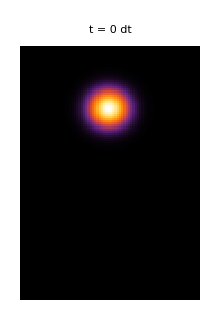
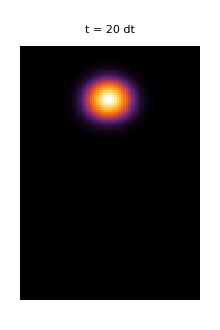
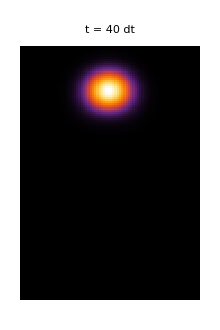
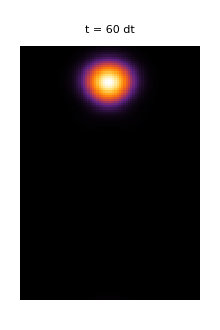
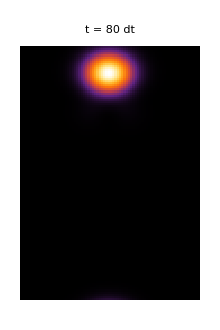
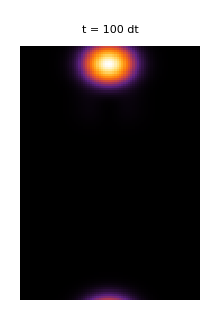
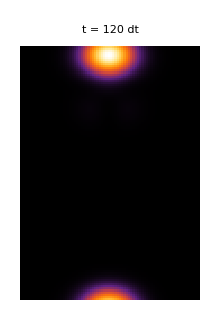
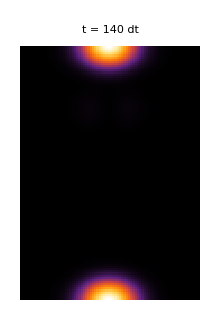

Transmitted fraction at t_final: 0.984651

Final norm (should be ~1): 1.

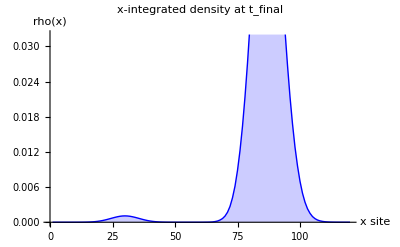

```mathematica
(* Use whichever snapshots you computed: snaps (Section 6) or snapsC (Section 6b) *)
snapData = If[Length[snaps] > 1, snaps, snapsC];

densPlots = Table[
  ArrayPlot[
    snapData[[k, 2]],
    ColorFunction -> "SunsetColors",
    PlotLabel -> Style["t = " <> ToString[snapData[[k, 1]]] <> " dt", 12, Bold],
    FrameLabel -> {"y/a", "x/a"},
    ColorFunctionScaling -> True,
    ImageSize -> 220],
  {k, 1, Length[snapData]}];

Print[Row[densPlots, "  "]];

(* Transmitted probability (x > xBarR) *)
transmittedFraction[dens_] :=
  Total[dens[[xBarR + 1 ;;]], 2] / Total[dens, 2];

Print["Transmitted fraction at t_final: ",
  N[transmittedFraction[snapData[[-1, 2]]]]];

Print["Final norm (should be ~1): ", N[Total[snapData[[-1, 2]], 2]]];

(* 1D density profile along x at final time *)
Print[ListLinePlot[
  Total[snapData[[-1, 2]], {2}],
  PlotLabel -> Style["x-integrated density at t_final", 13],
  AxesLabel -> {"x site", "rho(x)"},
  PlotStyle -> {Thick, Blue},
  Filling -> Bottom]];
```

## Section 8: Dispersion surface (3D band plot)

-Graphics3D-

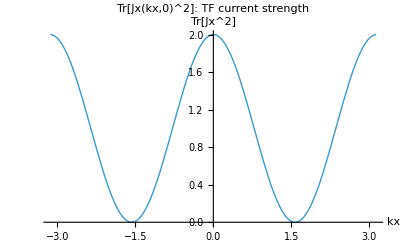

```mathematica
Print[Plot3D[
  2 Sqrt[Tan[kx/2]^2 + Tan[ky/2]^2],
  {kx, -Pi + 0.01, Pi - 0.01},
  {ky, -Pi + 0.01, Pi - 0.01},
  PlotLabel -> Style["TF Spin-1: positive band E(kx,ky)", 14, Bold],
  AxesLabel -> {"kx", "ky", "E"},
  ColorFunction -> "Rainbow",
  PlotRange -> {0, 8},
  Mesh -> None,
  ImageSize -> 420]];

(* Also plot the TF current magnitude |Jx| as a function of kx at ky=0 *)
Print[Plot[
  Tr[N[JxTF[kx, 0.0]].N[JxTF[kx, 0.0]]],  (* Tr[Jx^2] as proxy for magnitude *)
  {kx, -Pi + 0.01, Pi - 0.01},
  PlotLabel -> Style["Tr[Jx(kx,0)^2]: TF current strength", 13],
  AxesLabel -> {"kx", "Tr[Jx^2]"},
  PlotStyle -> {Thick}]];
```